```mathematica
(*Define parameters*)q=ω/gfb^2;

(*Matrices*)
A=ω {{0,1},{-1,0}};
B={{0,0},{0,1}};
K=ω {{0,0},{Sqrt[1+1/(ω q)]-1,Sqrt[1/(ω q)-2+2 Sqrt[1+1/(ω q)]]}};

(*Steady-state conditional variances*)
ξ=Sqrt[1+4 η Γ^2/ω^2];
Vxx=2/(Sqrt[2 η] Sqrt[ξ+1]);
Vpp=2 ξ/(Sqrt[2 η] Sqrt[ξ+1]);
Cxp=Sqrt[ξ-1]/(Sqrt[η] Sqrt[ξ+1]);

(*Noise vector and diffusion matrix*)
Gvec=Sqrt[2 η Γ] {Vxx,Cxp};
Dmat=Outer[Times,Gvec,Gvec];

(*Drift matrix with feedback*)
M=A-B.K;

(*Solve Lyapunov equation:M.Σ+Σ.M^T+Dmat=0*)
Σ={{σxx,σxp},{σxp,σpp}};
lyapunov=M.Σ+Σ.Transpose[M]+Dmat;

sol=Solve[{lyapunov[[1,1]]==0,lyapunov[[1,2]]==0,lyapunov[[2,2]]==0},{σxx,σxp,σpp}]//FullSimplify;

Σsol=Σ/. sol[[1]]//FullSimplify;

(*Total unconditional variances*)
VxxTotal=Vxx+Σsol[[1,1]];
VppTotal=Vpp+Σsol[[2,2]];

(*Mean phonon number*)
nbar=(VxxTotal+VppTotal)/4-1/2//FullSimplify;
```

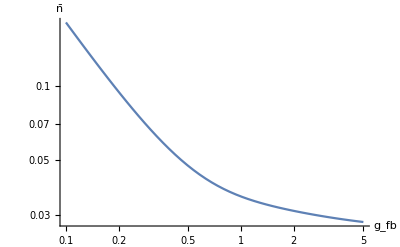

```mathematica
(*Set parameters and plot*)nbarPlot=nbar/. {ω->1,η->1,Γ->0.05};
Plot[nbarPlot,{gfb,0.1,5},AxesLabel->{"g_fb","n̄"},PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

```mathematica
nbar // FullSimplify
```

-1/2+1/4 ((√2)/(√η √(1+√(1+(4 Γ^2 η)/ω^2)))+(√(2+(8 Γ^2 η)/ω^2))/(√η √(1+√(1+(4 Γ^2 η)/ω^2)))+(Γ (-1+2 √(1+gfb^2/ω^2)+√(1+(4 Γ^2 η)/ω^2)))/((1+√(1+(4 Γ^2 η)/ω^2)) √(-2+2 √(1+gfb^2/ω^2)+gfb^2/ω^2) ω)+(2 gfb^2 Γ+Γ (-5+6 √(1+gfb^2/ω^2)+2 √2 √(-1+√(1+(4 Γ^2 η)/ω^2)) √(-2+2 √(1+gfb^2/ω^2)+gfb^2/ω^2)+√(1+(4 Γ^2 η)/ω^2)) ω^2)/((1+√(1+(4 Γ^2 η)/ω^2)) √(1+gfb^2/ω^2) √(-2+2 √(1+gfb^2/ω^2)+gfb^2/ω^2) ω^3))

```mathematica
Σsol // Simplify
```

{{(2 gfb^2 Γ+Γ (-5+6 √(1+gfb^2/ω^2)+2 √2 √(-1+√(1+(4 Γ^2 η)/ω^2)) √(-2+2 √(1+gfb^2/ω^2)+gfb^2/ω^2)+√(1+(4 Γ^2 η)/ω^2)) ω^2)/((1+√(1+(4 Γ^2 η)/ω^2)) √(1+gfb^2/ω^2) √(-2+2 √(1+gfb^2/ω^2)+gfb^2/ω^2) ω^3),-(2 Γ)/(ω+√(1+(4 Γ^2 η)/ω^2) ω)},{-(2 Γ)/(ω+√(1+(4 Γ^2 η)/ω^2) ω),(Γ (-1+2 √(1+gfb^2/ω^2)+√(1+(4 Γ^2 η)/ω^2)))/((1+√(1+(4 Γ^2 η)/ω^2)) √(-2+2 √(1+gfb^2/ω^2)+gfb^2/ω^2) ω)}}

```mathematica
Σsimple=Σsol//FullSimplify[#,Assumptions->{β>0,ω>0,η>0,Γ>0}]&
```

{{(Γ (2 gfb^2+ω (-5 ω+6 √(gfb^2+ω^2)+√(4 Γ^2 η+ω^2))+2 √2 √(-ω (ω-√(4 Γ^2 η+ω^2)) (gfb^2+2 ω (-ω+√(gfb^2+ω^2))))))/(√(gfb^2+ω^2) (ω+√(4 Γ^2 η+ω^2)) √(gfb^2+2 ω (-ω+√(gfb^2+ω^2)))),-(2 Γ)/(ω+√(4 Γ^2 η+ω^2))},{-(2 Γ)/(ω+√(4 Γ^2 η+ω^2)),(Γ (-ω+2 √(gfb^2+ω^2)+√(4 Γ^2 η+ω^2)))/((ω+√(4 Γ^2 η+ω^2)) √(gfb^2+2 ω (-ω+√(gfb^2+ω^2))))}}

```mathematica
Series[Σsol/. {gfb->ω/Sqrt[ε]},{ε,0,1}]//FullSimplify
```

{{(2 Γ)/(ω (1+√((4 Γ^2 η+ω^2)/ω^2)))+(2 Γ √(1/ε) √ε (2+√2 √(-1+√((4 Γ^2 η+ω^2)/ω^2))) √ε)/(ω (1+√((4 Γ^2 η+ω^2)/ω^2)))+(Γ (-7+√((4 Γ^2 η+ω^2)/ω^2)) ε)/(ω (1+√((4 Γ^2 η+ω^2)/ω^2)))+O[ε]^(3/2),-(2 Γ)/(ω+√(1+(4 Γ^2 η)/ω^2) ω)},{-(2 Γ)/(ω+√(1+(4 Γ^2 η)/ω^2) ω),(2 Γ)/(ω (1+√((4 Γ^2 η+ω^2)/ω^2)))+(Γ √(1/ε) √ε (-3+√((4 Γ^2 η+ω^2)/ω^2)) √ε)/(ω (1+√((4 Γ^2 η+ω^2)/ω^2)))-(Γ (-7+√((4 Γ^2 η+ω^2)/ω^2)) ε)/(ω (1+√((4 Γ^2 η+ω^2)/ω^2)))+O[ε]^(3/2)}}

```mathematica
Series[Σsol/. {gfb->Sqrt[ε] ω},{ε,0,1}]//FullSimplify
```

{{Γ/(√2 ω √ε)+(2 √2 Γ √(-1+√(1+(4 Γ^2 η)/ω^2)))/(ω+√(1+(4 Γ^2 η)/ω^2) ω)+(Γ (73-7 √(1+(4 Γ^2 η)/ω^2)) √ε)/(16 √2 (1+√(1+(4 Γ^2 η)/ω^2)) ω)-(√2 Γ √(-1+√(1+(4 Γ^2 η)/ω^2)) ε)/(ω+√(1+(4 Γ^2 η)/ω^2) ω)+O[ε]^(3/2),-(2 Γ)/(ω+√(1+(4 Γ^2 η)/ω^2) ω)},{-(2 Γ)/(ω+√(1+(4 Γ^2 η)/ω^2) ω),Γ/(√2 ω √ε)+(Γ (17+√(1+(4 Γ^2 η)/ω^2)) √ε)/(16 √2 (1+√(1+(4 Γ^2 η)/ω^2)) ω)+O[ε]^(3/2)}}